Compton scattering in particle-in-cell codes

Fabrizio del Gaudio, JPP
Notebook: Óscar Amaro, June 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

Outline
- Figure 3: Scattered photon distribution function f (analytical expression)
- Figure 4: Time evolution of the photon distribution (NDSolve)
- Stationary distributions

Figure 3: Scattered photon distribution function f

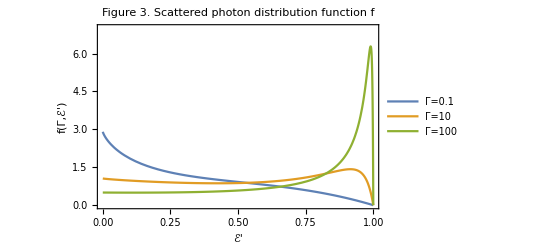

```mathematica
Clear[f,fnorm,Γ,q,ϵ]
f[Γ_,ϵ_]:=(2q Log[q]+(1+2q)(1-q)+1/2(Γ^2 q^2)/(1+Γ q)(1-q))/.{q->ϵ/(1+Γ(1-ϵ))}
fnorm[Γ_,ϵ_]:=f[Γ,ϵ]/NIntegrate[f[Γ,ϵϵ],{ϵϵ,0,1}]
Plot[{fnorm[0.1,ϵ],fnorm[10,ϵ],fnorm[100,ϵ]},{ϵ,0,1},PlotRange->{0,7},PlotLegends->{"Γ=0.1","Γ=10","Γ=100"},Frame->True,FrameLabel->{"ℰ'","f(Γ,ℰ')"},PlotLabel->"Figure 3. Scattered photon distribution function f"]
```

```mathematica
(*prove equivalence*)
Clear[u,x,t,exp1,exp2]
exp1=D[u[t,x],t]-D[x^2 D[u[t,x],x]+(x^2-2x)u[t,x],x]; (*eq 4.3*)
exp2=D[u[t,x],t]-x^2 (D[u[t,x],{x,1}]+D[u[t,x],{x,2}])-2(x-1)u[t,x];
exp1-exp2//Simplify
```

0

## Figure 4: Time evolution of the photon distribution

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

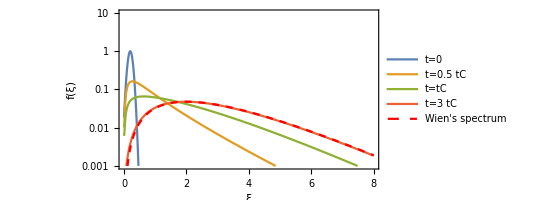

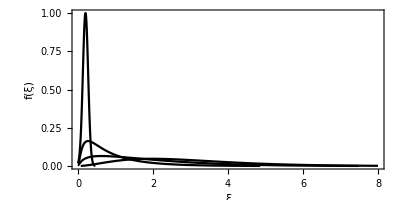

```mathematica
Clear[f,ξ,y,ξ0,σ0,pdeNL,pdeL,solNL,solL,tend,int]

(* parameters *)
ξ0=0.2;σ0=0.1;tend=3;ξend=20;

(*nonlinear version*)
pdeNL=-D[f[y,ξ],y]+2(ξ-1)D[f[y,ξ],{ξ,0}]+(ξ^2+2f[y,ξ])D[f[y,ξ],{ξ,1}]+(ξ^2)D[f[y,ξ],{ξ,2}]==0;
(*linear version*)
pdeL=-D[f[y,ξ],y]+2(ξ-1)D[f[y,ξ],{ξ,0}]+(ξ^2)D[f[y,ξ],{ξ,1}]+(ξ^2)D[f[y,ξ],{ξ,2}]==0;

solNL=NDSolve[{pdeNL,f[0,ξ]==Exp[-((ξ-ξ0)/σ0)^2],Derivative[0,0][f][y,0]==0,Derivative[0,0][f][y,ξend]==0},f[y,ξ],{y,0,tend},{ξ,0,ξend}];
solL=NDSolve[{pdeL,f[0,ξ]==Exp[-((ξ-ξ0)/σ0)^2],Derivative[0,0][f][y,0]==0,Derivative[0,0][f][y,ξend]==0},f[y,ξ],{y,0,tend},{ξ,0,ξend}];

(* normalize Wien spectrum *)
int=NIntegrate[Exp[-((ξξ-ξ0)/σ0)^2],{ξξ,0,∞}]/NIntegrate[ξξ^2Exp[-ξξ],{ξξ,0,∞}];
(* plot *)
LogPlot[{(solL/.{y->0,ξ-> ξξ})[[1,1,2]],(solL/.{y->0.5,ξ-> ξξ})[[1,1,2]],(solL/.{y->1,ξ-> ξξ})[[1,1,2]],(solL/.{y->3,ξ-> ξξ})[[1,1,2]],int ξξ^2Exp[-ξξ]},{ξξ,0,8},AspectRatio->1/2,PlotStyle->{Default,Default,Default,Default,Directive[Red,Dashed]},FrameStyle->Directive[Black],PlotRange->{{0,8},{10^-3,10^1}},Frame->True,FrameLabel->{"ξ","f(ξ)"},PlotLegends->{"t=0","t=0.5 tC","t=tC","t=3 tC","Wien's spectrum"}]

(* linear scale *)
Plot[{(solL/.{y->0,ξ-> ξξ})[[1,1,2]],(solL/.{y->0.5,ξ-> ξξ})[[1,1,2]],(solL/.{y->1,ξ-> ξξ})[[1,1,2]],(solL/.{y->3,ξ-> ξξ})[[1,1,2]]},{ξξ,0,8},AspectRatio->1/2,PlotStyle->Black,FrameStyle->Directive[Black],PlotRange->{{0,8},{10^-3,10^0}},Frame->True,FrameLabel->{"ξ","f(ξ)"}]
```

```mathematica
Manipulate[LogPlot[(solL/.{y->yy,ξ-> ξξ})[[1,1,2]],{ξξ,0,8},Frame->True,AspectRatio->1/2,PlotStyle->Black,FrameStyle->Directive[Black],PlotRange->{{0,8},{10^-3,1}},Frame->True,FrameLabel->{"ξ","f(ξ)"},PlotLabel->"Figure 4: dynamic evolution"],{yy,0,tend}]
```

Linear and nonlinear equilibrium solutions

See “A Practical Review of the Kompaneets Equation and its Application to Compton Scattering” by Donald G. Shirk

```mathematica
(* linear version *)
Clear[eq,n,x]
n=Exp[-x];
D[n,x]+n
(* Wien spectrum *)

(* nonlinear version include emission n^2*)
Clear[eq,n,x]
n=1/(Exp[+x]-1);
D[n,x]+n+n^2//Simplify
(* Bose Einstein spectrum *)
```

0

0

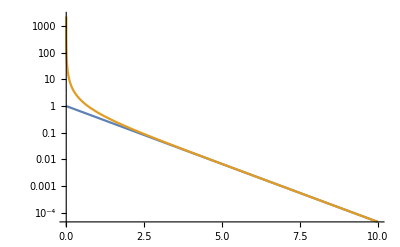

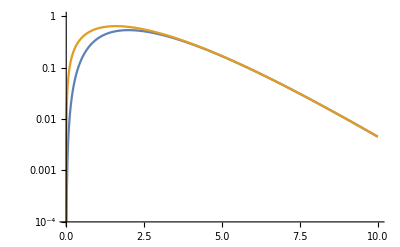

```mathematica
LogPlot[{1/(Exp[+x]),1/(Exp[+x]-1)},{x,0,10}]
(*Note: the plot is of f=ξ^2 n*)
LogPlot[{x^2/(Exp[+x]),x^2/(Exp[+x]-1)},{x,0,10}]
```